```mathematica
m1 = 40;
m2 = 20;
μ = m2/m1;
wz = 0.54078;
wip = √((1+μ-√(1-μ+μ^2))/μ)wz;
wop = √((1+μ+√(1-μ+μ^2))/μ)wz;
wip
wop
```

0.608936

1.17637

```mathematica
178.11+176.61
```

```mathematica
354.72/2
```

177.36

0.735

1.27306

```mathematica
m1 = 9;
m2 = 25;
μ = m2/m1;
wz = 0.735;
wip = √((1+μ-√(1-μ+μ^2))/μ)wz;
wop = √((1+μ+√(1-μ+μ^2))/μ)wz;
wip
wop
```

0.51067

1.09938

```mathematica
(6.626*10^-34*3*10^8)/(1.38*10^-23*300)
```

0.0000480145

```mathematica
1.38*10^-23*300/(6.626*10^-34)
```

6.24811×10^12

```mathematica
LaguerreL[5,0.01]
```

0.950498

```mathematica
(196.835+197.435)/2
```

197.135

```mathematica
√((86.8+89.2)/(24.6+41.0))*197.135
```

322.9

```mathematica
√(267/87.5)*338
```

590.43

```mathematica
√(((506+456)/2)/267)*598
```

598 √(481/267)

```mathematica
N[598 √(481/267)]
```

802.635

```mathematica
(24.6+41.0)/2
```

32.8

```mathematica
(86.8 + 89.2)/2
```

88.

```mathematica
(233.6 + 214.7)/2
```

224.15

```mathematica
(278.8 + 256.1)/2
```

267.45

```mathematica
freq={197.235,338,549,598}
```

{197.235,338,549,598}

```mathematica
voltage={32.8,88.,224.14999999999998,267.45000000000005}
```

{32.8,88.,224.15,267.45}

```mathematica
Plot[freq,voltage]
```

Plot::pllim: Range specification voltage is not of the form {x, xmin, xmax}.

Plot[freq,voltage]

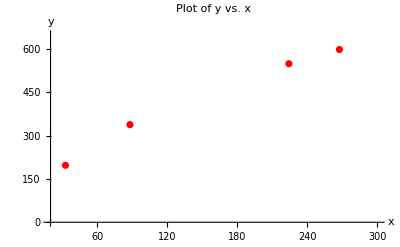

```mathematica
freq={197.235,338,549,598};voltage={32.8,88.,224.14999999999998,267.45000000000005};
ListPlot[Transpose[{voltage,freq}],AxesLabel->{"x","y"},PlotLabel->"Plot of y vs. x",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotStyle->Red]
```

General::ivar: 1 is not a valid variable.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

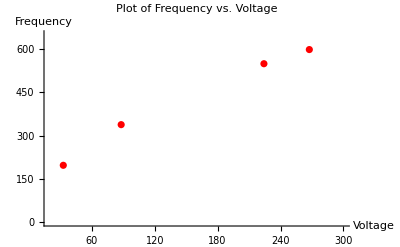

```mathematica
freq={197.235,338,549,598};
voltage={32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[x],C,x];

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,20,300}],AxesLabel->{"Voltage","Frequency"},PlotLabel->"Plot of Frequency vs. Voltage",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

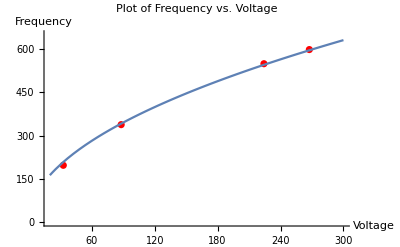

```mathematica
freq={197.235,338,549,598};
voltage={32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,20,300}],AxesLabel->{"Voltage","Frequency"},PlotLabel->"Plot of Frequency vs. Voltage",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
C
```

C

| Estimate | Standard Error | t-Statistic | P-Value
C | 36.4131 | 0.256924 | 141.727 | 1.48662×10^-8

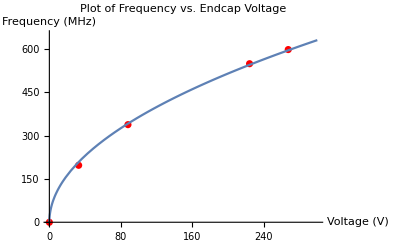

```mathematica
freq={0,197.235,338,549,598};
voltage={0,32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];
parameterTable=model["ParameterTable"]

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,0,300}],AxesLabel->{"Voltage (V)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Endcap Voltage\n",PlotRange->{{0,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
36.41308439480629*√800
```

1029.92

| Estimate | Standard Error | t-Statistic | P-Value
C | 36.4131 | 0.256924 | 141.727 | 1.48662×10^-8

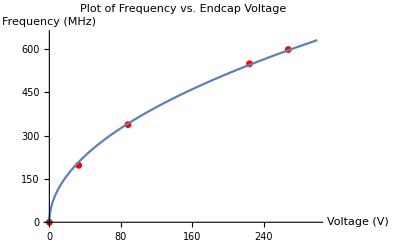

```mathematica
freq={0,197.235,338,549,598};
voltage={0,32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];
parameterTable=model["ParameterTable"]

Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,0,300}],AxesLabel->{"Voltage (V)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Endcap Voltage\n",PlotRange->{{0,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
5.1/322.9
```

0.0157944

```mathematica
9/540
```

1/60

```mathematica
N[1/60]
```

0.0166667

```mathematica
8/590
```

4/295

```mathematica
N[4/295]
```

0.0135593

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};
data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,Sqrt[C2*v-1/(√2)*36.41308439480629],C2,v];
parameterTable=model["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,0,3000}],AxesLabel->{"Voltage (V)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Endcap Voltage\n",PlotRange->{{0,3000},{0,6500}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

Transpose::nmtx: The first two levels of {voltage,{959,1772.25,2023.25,2436.25}} cannot be transposed.

NonlinearModelFit::fitd: First argument Transpose[{voltage,{959,1772.25,2023.25,2436.25}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Transpose[{voltage,{959,1772.25,2023.25,2436.25}}],√(-25.7479+C2 v),C2,v][ParameterTable]

Transpose::nmtx: The first two levels of {voltage,{959.,1772.25,2023.25,2436.25}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{voltage,{959.,1772.25,2023.25,2436.25}}] is not a list of numbers or pairs of numbers.

NonlinearModelFit::fitd: First argument Transpose[{voltage,{959,1772.25,2023.25,2436.25}}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Transpose[{voltage,{959.,1772.25,2023.25,2436.25}}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Transpose[{voltage,{959,1772.25,2023.25,2436.25}}],PlotStyle→color,PlotMarkers→{Automatic,7}],,AxesLabel→«1»,«1»,PlotRange→{{0,3000},{0,6500}},BaseStyle→{FontFamily→Helvetica,FontSize→12}].

Show[ListPlot[Transpose[{voltage,{959,1772.25,2023.25,2436.25}}],PlotStyle→RGBColor[1, 0, 0],PlotMarkers→{Automatic,7}],-Graphics-,AxesLabel→{Voltage (V),Frequency (MHz)},PlotLabel→Plot of Frequency vs. Endcap Voltage
,PlotRange→{{0,3000},{0,6500}},BaseStyle→{FontFamily→Helvetica,FontSize→12}]

NonlinearModelFit::optx: Unknown option Constraints in NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},Re[√(-25.7479+C2 v)],C2,v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0,v>0}].

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},Re[√(-25.7479+C2 v)],C2,v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0,v>0}][ParameterTable]

NonlinearModelFit::optx: Unknown option Constraints in NonlinearModelFit[{{3.,959.},{5.,1772.25},{7.,2023.25},{10.,2436.25}},Re[√(-25.7479+C2 v)],C2,v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0.,v>0.}].

General::stop: Further output of NonlinearModelFit::optx will be suppressed during this calculation.

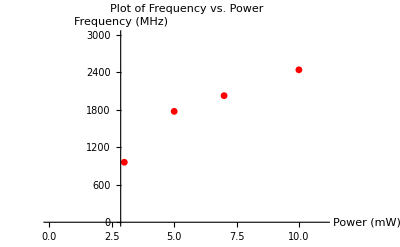

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};
data=Transpose[{power,freq}];
model=NonlinearModelFit[data,Re[Sqrt[C2*v-1/Sqrt[2]*36.41308439480629]],C2,v,Method->{NMinimize,Method->"NelderMead"},Constraints->{C2>0,v>0}];
parameterTable=model["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,0,11}],AxesLabel->{"Power (mW)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Power\n",PlotRange->{{0,11},{0,3000}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

NonlinearModelFit::optx: Unknown option ParameterRanges in NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√(-25.7479+C2 v),{C2,v},v,Method→{NMinimize,Method→NelderMead},ParameterRanges→{C2>0,v>0}].

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√(-25.7479+C2 v),{C2,v},v,Method→{NMinimize,Method→NelderMead},ParameterRanges→{C2>0,v>0}][ParameterTable]

NonlinearModelFit::optx: Unknown option ParameterRanges in NonlinearModelFit[{{3.,959.},{5.,1772.25},{7.,2023.25},{10.,2436.25}},√(-25.7479+C2 v),{C2,v},v,Method→{NMinimize,Method→NelderMead},ParameterRanges→{C2>0.,v>0.}].

General::stop: Further output of NonlinearModelFit::optx will be suppressed during this calculation.

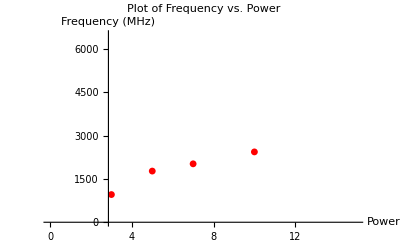

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};
data=Transpose[{power,freq}];
model=NonlinearModelFit[data,Sqrt[C2*v-1/Sqrt[2]*36.41308439480629],{C2,v},v,Method->{NMinimize,Method->NelderMead},ParameterRanges->{C2>0,v>0}];
parameterTable=model["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,0,15}],AxesLabel->{"Power","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Power\n",PlotRange->{{0,15},{0,6500}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14280={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14317={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14338={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14359={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√(-25.7479+C2 v),{C2,v},v,Method→{NMinimize,Method→NelderMead}][ParameterTable]

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14694={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14713={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

NonlinearModelFit::nrnum: The function value 7.04463×10^6-31556.8 ⅈ is not a real number at {C2,v} = {0.918621,0.716689}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{0.716689={3.,5.,7.,10.},Optimization`FindFit`y$14732={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-«28»).(«1»)]],Block},«4»,{«1»}][{«1»}] is not a number at {C2,v} = {0.918621,0.716689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

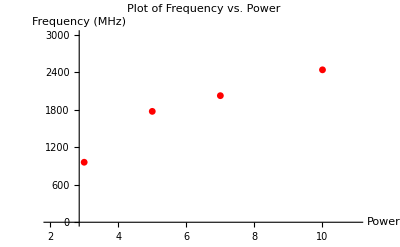

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};
data=Transpose[{power,freq}];
model=NonlinearModelFit[data,Sqrt[C2*v-1/Sqrt[2]*36.41308439480629],{C2,v},v,Method->{NMinimize,Method->NelderMead}];
parameterTable=model["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,2,11}],AxesLabel->{"Power","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Power\n",PlotRange->{{2,11},{0,3000}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};
data=Transpose[{power,freq}];
model=NonlinearModelFit[data,Sqrt[Max[C2*v-1/Sqrt[2]*36.41308439480629,0]],{C2,v},v,Method->{NMinimize,Method->NelderMead},Constraints->{C2>0,v>0}]
parameterTable=model["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,2,11}],AxesLabel->{"Power","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Power\n",PlotRange->{{2,11},{0,3000}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

NonlinearModelFit::optx: Unknown option Constraints in NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√Max[0,-25.7479+C2 v],{C2,v},v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0,v>0}].

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√Max[0,-25.7479+C2 v],{C2,v},v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0,v>0}]

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√Max[0,-25.7479+C2 v],{C2,v},v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0,v>0}][ParameterTable]

NonlinearModelFit::optx: Unknown option Constraints in NonlinearModelFit[{{3.,959.},{5.,1772.25},{7.,2023.25},{10.,2436.25}},√Max[0.,-25.7479+C2 v],{C2,v},v,Method→{NMinimize,Method→NelderMead},Constraints→{C2>0.,v>0.}].

General::stop: Further output of NonlinearModelFit::optx will be suppressed during this calculation.

-Graphics-

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};

data=Transpose[{power,freq}];
model=NonlinearModelFit[data,Sqrt[C2*p-1/Sqrt[2]*36.41308439480629],C2,p,Method->{NMinimize,Method->NelderMead}];
parameterTable=model["ParameterTable"]

Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,2,11}],AxesLabel->{"Power","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Power\n",PlotRange->{{2,11},{0,3000}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$21950={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$21950).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$21967={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$21967).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$21984={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$21984).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$22005={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$22005).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit[{{3,959},{5,1772.25},{7,2023.25},{10,2436.25}},√(-25.7479+C2 p),C2,p,Method→{NMinimize,Method→NelderMead}][ParameterTable]

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$22346={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$22346).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$22365={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$22365).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

NonlinearModelFit::nrnum: The function value 7.04461×10^6-40363.8 ⅈ is not a real number at {C2} = {-0.829053}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{p={3.,5.,7.,10.},Optimization`FindFit`y$22386={959.,1772.25,2023.25,2436.25}},1/2 (Power[«2»]-Optimization`FindFit`y$22386).(«1»)]],Block},«5»][{-«19»}] is not a number at {C2} = {-0.829053}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

-Graphics-

{c1→-1.17258×10^6,c2→749573.}

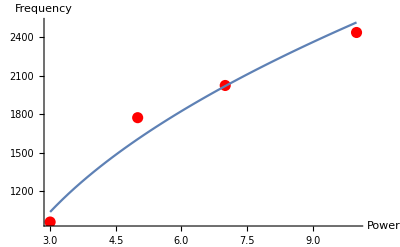

{c1→-1.17258×10^6,c2→749573.}

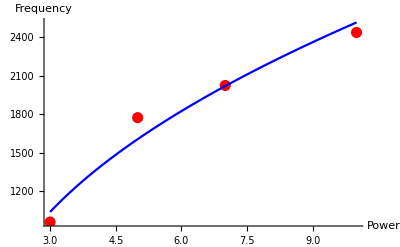

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};

fit=FindFit[Transpose[{power,freq}],Sqrt[c2*x+c1],{c1,c2},x]

Show[ListPlot[Transpose[{power,freq}],PlotStyle->{Red,PointSize[0.02]}],Plot[Sqrt[c2*x+c1]/. fit,{x,0,Max[power]},BaseStyle->{FontFamily->"Helvetica",FontSize->12}],AxesLabel->{"Power","Frequency"},PlotRange->All]
```

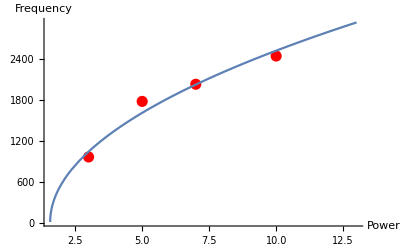

```mathematica
freq={959,1772.245,2023.245,2436.245};
power={3,5,7,10};

fit=FindFit[Transpose[{power,freq}],Sqrt[c2*x+c1],{c1,c2},x];

Show[ListPlot[Transpose[{power,freq}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{0,13},{0,All}}],Plot[Sqrt[c2*x+c1]/. fit,{x,0,13},BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotRange->{{0,13},{0,All}}],AxesLabel->{"Power","Frequency"},PlotRange->All]
```

```mathematica
5000/(2*10^8)+5000/(3*10^8)
```

1/24000

```mathematica
N[1/24000]
```

0.0000416667

```mathematica
N[1250000000000/3]
```

4.16667×10^11

```mathematica
√(4*10^-5*2)
```

1/(50 √5)

```mathematica
N[1/(50 √5)]
```

0.00894427

```mathematica
0.00894427190999916*0.33333/0.7
```

0.00425913

```mathematica
0.0042591345082286*200000
```

851.827

```mathematica
0.00894427190999916*200000
```

1788.85

```mathematica
0.00894427190999916*10000
```

89.4427

```mathematica
4*10^-5*10000
```

2/5

```mathematica
6.8/92
```

0.073913

```mathematica
(0.021+0.024)/2
```

0.0225

```mathematica
0.068*0.0225*0.87*0.45*200000
```

119.799

```mathematica
0.0225*0.87*0.45*200000
```

1761.75

```mathematica
0.068*0.0225*0.87*0.45*20000
```

11.9799

```mathematica
0.5*(0.068*0.0225*0.87*0.45)^2*10000
```

0.00179398

```mathematica
0.5
```

0.5

```mathematica
0.0225*0.87*0.45*200000
```

1761.75

```mathematica
0.0225*0.87*0.45*10000
```

88.0875

```mathematica
1/2*(0.0225*0.87*0.45)^2*200000
```

7.75941

```mathematica
1/2*(0.0225*0.87*0.45)^2*10000
```

0.38797

```mathematica
(*Summary of Calculation, ion-fibre couplings 0.5, the coupling efficiency into the single mode fibre preceding the detector 0.9, quantum efficiency 0.65, total measured collection efficiency 0.0225*)
```

```mathematica
0.0225*0.87*0.45*200000
```

1761.75

```mathematica
0.0225*0.87*0.45*10000
```

88.0875

```mathematica
0.0225*0.87*0.10*200000
```

391.5

```mathematica
0.0225*0.87*0.10*10000
```

19.575

```mathematica
1/2*(0.0225*0.87*0.10)^2*200000
```

0.383181

```mathematica
1/2*(0.0225*0.87*0.10)^2*10000
```

0.019159

```mathematica
1/2*(0.0225*0.87*0.45)^2*200000*0.5*0.07
```

0.271579

```mathematica
1/2*(0.0225*0.87*0.45)^2*10000*0.5*0.07
```

0.013579